# Rapport projekt 1

Sushil K C, XXXX, sushilkc@kth.se
 Sebastian Rone, XXXX, sebgro@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Hitta lösningarna till polynomekvationen: 2 x^4+28/3 x^3-22/3 x^2-140/3 x+16=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Resultat

För att hitta lösningarna till polynomekvationen: 2 x^4+28/3 x^3-22/3 x^2-140/3 x+16=0. 
Använder jag funktionen Solve[] där den ska lösa variabeln x.

```mathematica
{x1,x2,x3,x4}=x/.Solve[2 x^4+28/3 x^3-22/3 x^2-140/3 x+16==0]
```

{-4,-3,1/3,2}

Jag använder x1, x2 ... för att spara ekvationens nollställen/skärningspunkter på de värderna för att sedan använda dem när jag ska rita grafen.

För att plotta grafen används funktionen Plot, där jag använder Axeslabel för att ge horisontal planet namnet x och vertikal planet till y. Epilog används för att få punkter på nollställena där efter väljer jag färgen röd samt punkternas storlek och vart punkterna ska vara någonstans (Point)

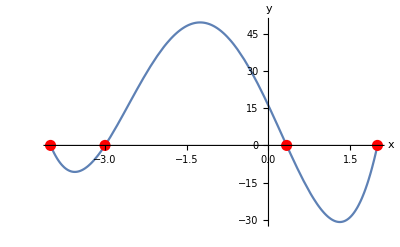

```mathematica
Plot[2 x^4+(28 x^3)/3-(22 x^2)/3-(140 x)/3+16,{x,2,-4},AxesLabel->{"x","y"},Epilog ->{Red,PointSize[0.02],
Point[{x1,0}],
Point[{x2,0}],
Point[{x3,0}],
Point[{x4,0}]
}
]
```

## Vägbygge

### Modell för tvärsnittsarea

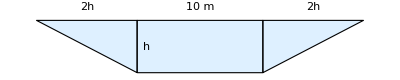

Den givna parallelltrapetsen har arean

a(h)=(10+2h)h

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

Med hjälp av data interpoleras en funktion A(x).

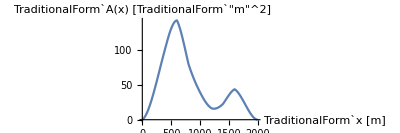

### Modell för volym

Den efterfrågade volym som ska transporteras bort kan beräknas numeriskt ned integralen

V=∫_0^2000 A(x)dx

V≈101 10^3 m^3

Dvs. ca 100 tusen m^3 måste borttransporteras.

## Kod

```mathematica
ClearAll["`*"]
```

Givna data införs

```mathematica
𝕙={0,2.6,5.1,6.3,4.3,2.6,1.3,1.7,2.8,1.5,0};
𝕩=Range[0,2000,200];
```

Tvärsnittsarean definieras som funktion av höjden

```mathematica
a0[h_]:=(10+2h)h
```

Data för a(x) tabelleras:

```mathematica
data=Transpose[{𝕩,a0[𝕙]}]
```

{{0,0},{200,39.52},{400,103.02},{600,142.38},{800,79.98},{1000,39.52},{1200,16.38},{1400,22.78},{1600,43.68},{1800,19.5},{2000,0}}

```mathematica
TableForm[Transpose[{𝕩,𝕙,a0[𝕙]}],TableHeadings->{None,{"x [m]","h [m]","a [m^2]"}}]
```

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

Funktionen a(x) kan nu interpoleras:

```mathematica
a=Interpolation[data]
```

InterpolatingFunction[…]

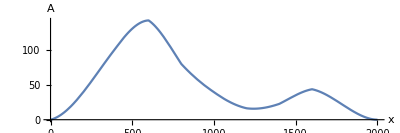

```mathematica
Plot[a[x],{x,0,2000},AxesLabel->{x,A},AspectRatio->1/3]
```

Slutligen kan den efterfrågade volymen beräknas.

```mathematica
NIntegrate[a[x],{x,0,2000}]
```

101281.

Uppgift 2: Olikhet

## Sammanfattning

### Uppgift

Lös uppgift 21, 22 och 26  i kapitel 3 i boken Matematisk kommunikation, argumentation och skapande. Ge ett exakt svar. I de fall det är lämpligt illustrera lösningsområdet grafiskt.

### Resultat

##### Uppgift 21

```mathematica
Reduce[ {(x-2)/(x^2+1)>=0}, x, Reals]
```

x≥2

```mathematica
Reduce[{2/(3x-1)<=1}, x,Reals]
```

x<1/3||x≥1

```mathematica
Reduce[{4/(x^2+4)>=1/2}, x, Reals]
```

-2≤x≤2

```mathematica
Reduce[{(x-2)/(x^2-1)>=0},x,Reals]
```

-1<x<1||x≥2

```mathematica
Reduce[{(x-2)/(x-1)>=1+(2x)/(x+1)}, x,Reals]
```

-1<x<1

##### Uppgift 22

```mathematica
Reduce[{Sqrt[x+1]<= - Sqrt[(2+x)]},x,Reals]
```

False

```mathematica
Reduce[{Sqrt[2x-1]>- Sqrt[(3-x)]},x,Reals]
```

1/2≤x≤3

```mathematica
Reduce[{Sqrt[x^2-1]>= Sqrt[2x^2-2x]},x,Reals]
```

x==1

```mathematica
Reduce[{2+Sqrt[x]>= x},x,Reals]
```

0≤x≤4

##### Uppgift 26

```mathematica
Reduce[Abs[x-1]+Abs[x-2]==5,x,Reals]
```

x==-1||x==4

```mathematica
Reduce[Abs[x^2-x-2]==2,x,Reals]
```

x==0||x==1||x==1/2 (1-√17)||x==1/2 (1+√17)

## Sparklängd

### Lösning av differentialekvationerna

Vinkeln θ ansätts vilket ger initialvärden (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Därefter löses differentialekvationerna

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

löses numeriskt.

### Bestämning av sparktid och sparklängd

Tiden t_0 bestäms så att y(t_0)=0. Slutligen bestäms sparklängden L=x(t_0).

Ovanstående procedur repeteras för olika vinklar och därefter interpoleras en funktion L(θ) vars maximum bestäms

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

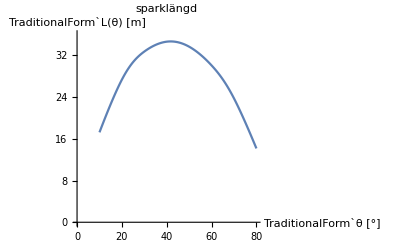

En funktion interpoleras L(θ) vars maximum bestäms

L_max≈35m, θ_max≈41°

## Kod

```mathematica
ClearAll["`*"]
```

Inför givna data

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Definiera diff.ekvationer och begynnelsevillkor.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Lös diff.ekv.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Exempel för θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

Kurva för variabel vinkel

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

Funktion för sparklängd

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Exempel

```mathematica
len[45°]
```

Tabell för olik vinklar

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Noggrannare data kring maxvärdet.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Sök maxvärde

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```

Uppgift 3: Binomisk ekvation

## Sammanfattning

### Uppgift

Finn lösningen till ekvationenz^5=-3+3ioch visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

```mathematica
För att hitta lössningarna till den komplexa ekvationen: z=-3+3i
```

att den För hitta komplexa lössningarna till (ekvationen:-3+3 i)

```mathematica
{z1,z2,z3,z4,z5}=z/.Solve[z^5 == -3 + 3*I]
```

```mathematica
{-3+3 Root"0.560"+"0.0696" ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,1}]0.560432147724209,-3+3 Root"0.798"-"0.397" ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,2}]0.797952835199128,-3+3 Root"0.930"+"0.440" ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,3}]0.9303792917326404,-3+3 Root"1.31"-"0.315" ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,4}]1.3146958370983006,-3+3 Root"1.40"+"0.202" ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,5}]1.3965398882457218}
```

```mathematica
cn={N[z1],N[z2],N[z3],N[z4],N[z5]}
```

{-1.3187+0.208862 ⅈ,-0.606141-1.18962 ⅈ,-0.208862+1.3187 ⅈ,0.944088-0.944088 ⅈ,1.18962+0.606141 ⅈ}

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i, 1, 5}]
```

```mathematica
{{-1.3187035568273728,0.20886212480207877},{-0.6061414944026162,-1.1896196647371657},{-0.20886212480207877,1.3187035568273728},{0.9440875112949021,-0.9440875112949021},{1.1896196647371653,0.6061414944026161}}
z1 = -1.3187035568273728+0.20886212480207877I
```

{{-1.3187,0.208862},{-0.606141,-1.18962},{-0.208862,1.3187},{0.944088,-0.944088},{1.18962,0.606141}}

-1.3187+0.208862 ⅈ

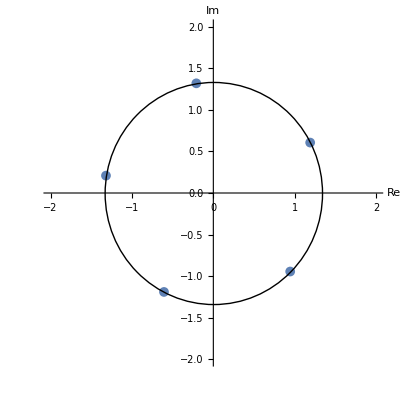

```mathematica
ListPlot[pp, PlotRange ->{{-2,2},{-2,2}}, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ EdgeForm[Red],FaceForm[],Circle[{0,0 },Abs[z1]]}]
```

## Sparklängd

### Lösning av differentialekvationerna

Vinkeln θ ansätts vilket ger initialvärden (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Därefter löses differentialekvationerna

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

löses numeriskt.

### Bestämning av sparktid och sparklängd

Tiden t_0 bestäms så att y(t_0)=0. Slutligen bestäms sparklängden L=x(t_0).

Ovanstående procedur repeteras för olika vinklar och därefter interpoleras en funktion L(θ) vars maximum bestäms

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

-Graphics-

En funktion interpoleras L(θ) vars maximum bestäms

L_max≈35m, θ_max≈41°

## Kod

```mathematica
ClearAll["`*"]
```

Inför givna data

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Definiera diff.ekvationer och begynnelsevillkor.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Lös diff.ekv.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Exempel för θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

Kurva för variabel vinkel

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

Funktion för sparklängd

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Exempel

```mathematica
len[45°]
```

Tabell för olik vinklar

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Noggrannare data kring maxvärdet.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Sök maxvärde

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```

Uppgift 4: Arean av en cirkel och närmevärde till Pi

## Sammanfattning

### Uppgift

En kvadrat kan skrivas in i en cirkel och en cirkel kan skrivas in i en kvadrat, vilket ger figuren nedan. Antag att cirkeln har radien r=1.

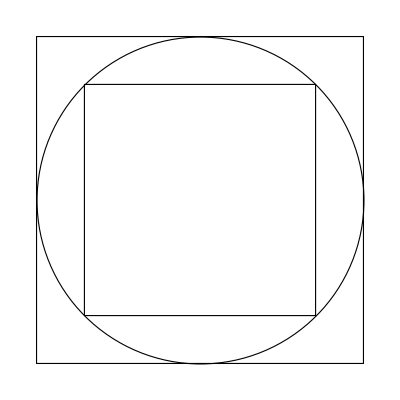

```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
```

Från figuren kan vi konstatera att cirkelns area är mindre än 2^2=4 och större än (2/√2)^2=2. Det betyder att vi kan bestämma π=3±1. Dvs medelvärdet av 4+2 och det absoluta felet till närmevärdet. Då cirkelns area i detta fall är π r^2= π, så är detta också en metod att bestämma ett närmevärde till π. 
Vi kan också se arean för en kvadrat som fyrsidig polygon där arean kan bestämmas av fyra trianglar.
Använd ovanstående metod med reglebundna polygoner med fler sidor än fyra och beräkna ett mer exakt värde på π. Jämför sedan med värdet på Pi i Mathematica (se nedan med 10 siffor). Du får använda trigonometriska funktioner för att bestämma arean av trianglarna. 
Rita en graf för hur min och max värdet konvergerar mot Pi som en funktion av antal sidor på polygonen.

```mathematica
N[Pi, 10]
```

3.141592654

### Resultat

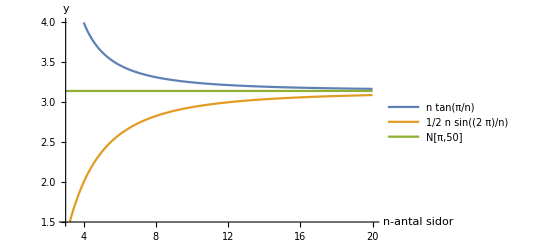

```mathematica
Plot[{n*Tan[Pi/n],(n*Sin[2Pi/n])/2, N[Pi,50]}, {n,3, 20},PlotRange->{1.5,4}, AxesLabel->{"n-antal sidor","y"}, PlotLegends->"Expressions"]
```

## Sparklängd

### Lösning av differentialekvationerna

Vinkeln θ ansätts vilket ger initialvärden (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Därefter löses differentialekvationerna

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

löses numeriskt.

### Bestämning av sparktid och sparklängd

Tiden t_0 bestäms så att y(t_0)=0. Slutligen bestäms sparklängden L=x(t_0).

Ovanstående procedur repeteras för olika vinklar och därefter interpoleras en funktion L(θ) vars maximum bestäms

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

-Graphics-

En funktion interpoleras L(θ) vars maximum bestäms

L_max≈35m, θ_max≈41°

## Kod

```mathematica
ClearAll["`*"]
```

Inför givna data

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Definiera diff.ekvationer och begynnelsevillkor.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Lös diff.ekv.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Exempel för θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

Kurva för variabel vinkel

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

Funktion för sparklängd

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Exempel

```mathematica
len[45°]
```

Tabell för olik vinklar

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Noggrannare data kring maxvärdet.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Sök maxvärde

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```